# Les polynômes de Laguerre

## Définision du produit scalaire

### Fonction poid

```mathematica
w:=ⅇ^-x
```

### Intervalle d’orthogonalité

```mathematica
a:=0
```

```mathematica
b:=+∞
```

### Produit scalaire

```mathematica
⟨f_|g_⟩:=∫_a^b w f gⅆx
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Base

### Base orthogonale

```mathematica
dim:=5
```

```mathematica
Subscript[n, min]:=0;Subscript[n, max]:=dim-1;
```

```mathematica
Subscript[𝓊, n_][x_]:=LaguerreL[n,x]
```

```mathematica
Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]//TableForm//TraditionalForm
```

1
1-x
1/2 (x^2-4 x+2)
1/6 (-x^3+9 x^2-18 x+6)
1/24 (x^4-16 x^3+72 x^2-96 x+24)

```mathematica
orthogonality[Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

### Représentation graphique

```mathematica
Subscript[x, min]:=0;Subscript[x, max]:=5;
```

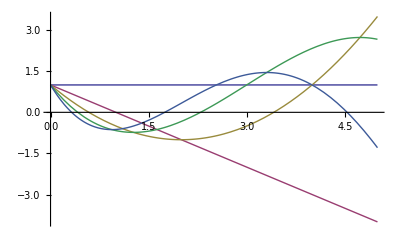

```mathematica
Plot[Evaluate[Table[Subscript[𝓊, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

### Base orthonormale

On peut normaliser cette base

```mathematica
Subscript[𝓊̃, n_][x_]:=normalize[Subscript[𝓊, n][x]]
```

```mathematica
Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]//Simplify//TableForm//TraditionalForm
```

1
1-x
1/2 (x^2-4 x+2)
-x^3/6+(3 x^2)/2-3 x+1
x^4/24-(2 x^3)/3+3 x^2-4 x+1

```mathematica
orthogonality[Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]]
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

### Représentation graphique

```mathematica
Plot[Evaluate[Table[Subscript[𝓊̃, n][x],{n,Subscript[n, min],Subscript[n, max]}]],{x,Subscript[x, min],Subscript[x, max]}]
```

-Graphics-

## Développement

### La fonction à développer

```mathematica
f[x]:=x^3
```

### Les coeficients de Fourier

```mathematica
Subscript[a, n_]:=⟨Subscript[𝓊̃, n][x]|f[x] ⟩
```

```mathematica
Table[Subscript[a, n],{n,Subscript[n, min],Subscript[n, max]}]//Simplify
```

{6,-18,18,-6,0}

### Dévelopement de f(x) sur la base orthonormale

```mathematica
∑_(n=0)^10 Subscript[a, n] Subscript[𝓊̃, n]
```

6 (𝓊̃)_0-18 (𝓊̃)_1+18 (𝓊̃)_2-6 (𝓊̃)_3

```mathematica
Manipulate[∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][x],{N,0,10,1}]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^N Subscript[a, n] Subscript[𝓊̃, n][x]}],{x,Subscript[x, min],Subscript[x, max]},PlotRange->All],{N,0,10,1},ControlType->Setter]
```